```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
HSTdata = Import[NotebookDirectory[]<>"UVLF_HST.txt","Table"];
DeleteDuplicates[HSTdata[[3;;-1,1]]]
ΦHST[z_]:=Select[HSTdata[[3;;-1]],#[[1]]==z&][[All,{2,4,5}]]
Harikanedata = Import[NotebookDirectory[]<>"UVLF_Harikane.txt","Table"];
DeleteDuplicates[Harikanedata[[3;;-1,1]]]
ΦHarikane[z_]:=Select[Harikanedata[[3;;-1]],#[[1]]==z&][[All,{2,3,4,5}]]
```

{4,5,6,7,8,9,10}

{4.,5.,6.,7.}

```mathematica
hmf = ReadList[NotebookDirectory[]<>"hmf.dat",Table[Number,{8}]];
hmfi = Interpolation[{#[[1]],#[[2]],#[[3]]}&/@hmf];
dotMi = Interpolation[{#[[1]],#[[2]],#[[4]]}&/@hmf];
DdotMi = Interpolation[{#[[1]],#[[2]],#[[5]]}&/@hmf,InterpolationOrder->1];
phiUVi = Interpolation[{#[[1]],#[[6]],#[[8]]}&/@hmf,InterpolationOrder->1];
AUVi = Interpolation[{#[[1]],#[[6]],#[[7]]}&/@hmf,InterpolationOrder->1];
```

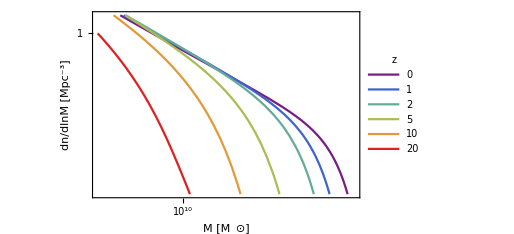

```mathematica
Plot[Log10[10^9hmfi[#,10^logM]]&/@{0.01,1,2,5,10,20}//Evaluate,{logM,7,Log10@hmfi[[1,2,2]]},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,1}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,5]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,1,2,5,10,20},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]]
```

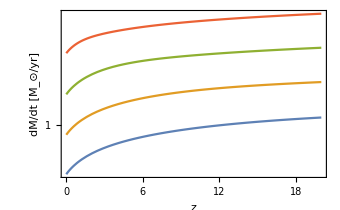

```mathematica
Plot[10^-6*dotMi[z,10^#]&/@Range[8,14,2]//Log10//Evaluate,{z,dotMi[[1,1,1]],20},FrameLabel->{"z","dM/dt ["<>Msunt<>"/yr]"},FrameTicks->{{logticksx,logticksx2},Automatic},ImageSize->340]
```

```mathematica
find0[X_]:=Module[{Xmax,jcut},
Xmax = First@First@MaximalBy[X,Last];
jcut = First@Flatten@Position[Select[X,#[[1]]>Xmax&],0];
X[[1;;jcut]]
]
```

```mathematica
Plnmulist = ReadList[NotebookDirectory[]<>"Plnmu.dat",Table[Number,{3}]];
zlist = DeleteDuplicates[Plnmulist[[All,1]]]
Plnmulist =GatherBy[Plnmulist,First][[All,All,{2,3}]];
Plnmui = Interpolation[find0[#],InterpolationOrder->1]&/@Plnmulist;
```

{0.5,1,2,3,4,5,6,7,8,9,10}

```mathematica
Plnmuf=Table[Function[lnmu,Piecewise[{{Plnmui[[j]][lnmu],Plnmui[[j]][[1,1,1]]<lnmu < Plnmui[[j]][[1,1,2]]}},0]//Evaluate],{j,Length@Plnmui}];
```

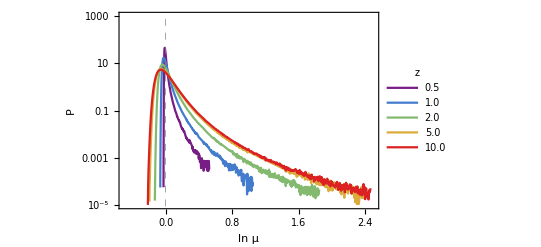

```mathematica
LogPlot[#[x]&/@Plnmuf[[{1,2,3,6,11}]]//Evaluate,{x,-0.5,10},PlotRange->{{-0.5,2.5},{1.*^-5,1000}},GridLines->{{0},{}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"ln μ","P"},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),PlotLegends->LineLegend[Automatic,{"0.5","1.0","2.0","5.0","10.0"},LegendMarkerSize->{10,4},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendLabel->Style["z",14]]]
```

```mathematica
phiUV1 = Table[{#,Quiet@phiUVi[zlist[[jz]],#-AUVi[zlist[[jz]],#]]}&/@Subdivide[-24.,-15,31],{jz,Length@zlist}];
phiUV2 = Table[{#,Quiet@NIntegrate[phiUVi[zlist[[jz]],#-AUVi[zlist[[jz]],#]+Log[10]lnmu]Plnmuf[[jz]][lnmu],{lnmu,-0.4,2.5},Method->"AdaptiveMonteCarlo"]}&/@Subdivide[-26.,-15,31],{jz,Length@zlist}];
```

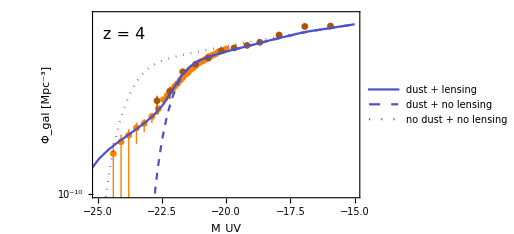

```mathematica
jz0 = 5;z0 = zlist[[jz0]];
Legended[Show[
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[3]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@ΦHarikane[z0]//Evaluate,PlotStyle->Orange,PlotRange->{{-25,-15},{-10,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->380],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[3]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@ΦHST[z0]//Evaluate,PlotStyle->Darker@Orange],
Plot[Log10[10^9phiUVi[z0,m-AUVi[z0,m]]]//Evaluate,{m,-26,-15},PlotStyle->Directive[RGBColor[0.3,0.32,0.78],Dashed]],
Plot[Log10[10^9phiUVi[z0,m]]//Evaluate,{m,-26,-15},PlotStyle->Directive[RGBColor[0.3,0.32,0.78],Dotted]],
ListPlot[{#[[1]],Log10[10^9#[[2]]]}&/@phiUV2[[jz0]],Joined->True,PlotStyle->RGBColor[0.3,0.32,0.78]],
Graphics[Text[Style["z = "<>ToString@z0,16],Scaled@{0.12,0.88}]]
],Placed[LineLegend[{RGBColor[0.3,0.32,0.78],Directive[RGBColor[0.3,0.32,0.78],Dashed],Directive[RGBColor[0.3,0.32,0.78],Dotted]},{"dust + lensing","dust + no lensing","no dust + no lensing"},LabelStyle->{FontSize->14,FontFamily->"Times"},LegendMarkerSize->{24,4}],Scaled@{0.72,0.25}]]
```

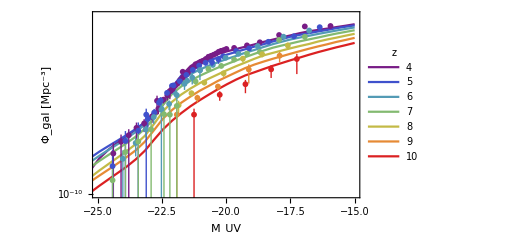

```mathematica
Show[
ListPlot[Table[{#[[1]],Log10[10^9#[[2]]]}&/@phiUV2[[j]],{j,Range[5,11,1]}],Joined->True,PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6]),PlotLegends->LineLegend[Automatic,{4,5,6,7,8,9,10},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]],PlotRange->{{-25,-15},{-10,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6]),ImageSize->380],
ListPlot[Table[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[3]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@ΦHST[z],{z,{4,5,6,7,8,9,10}}]//Evaluate,PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6])],
ListPlot[Table[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[3]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@ΦHarikane[z],{z,{4,5,6,7}}]//Evaluate,PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,6])]]
```